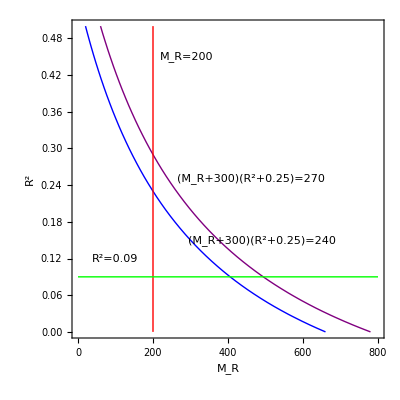

```mathematica
cp = ContourPlot[{(x+300)(y+0.25)==240,(x+300)(y+0.25)==270,x==200,y==0.09},{x,0,800},{y,0,0.5},FrameLabel->{Subscript[M, R],R^2},FrameStyle->20,ContourStyle->{Blue,Purple,Red,Green}];

Show[cp,Graphics[Text["(M_R+300)(R^2+0.25)=270",{460,0.25},Background->White,BaseStyle->{15,FontColor->Purple}]],Graphics[Text["(M_R+300)(R^2+0.25)=240",{490,0.15},Background->White,BaseStyle->{15,FontColor->Blue}]],Graphics[Text["R^2=0.09",{100,0.12},BaseStyle->{15,FontColor->Green}]],
Graphics[Text["M_R=200",{290,0.45},BaseStyle->{15,FontColor->Red}]]]
```